-Graphics3D-

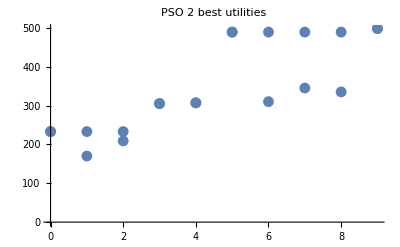

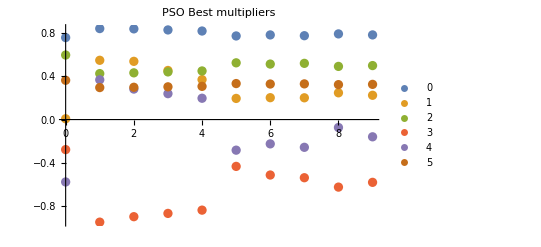

Import::nffil: File not found during Import.

ListPointPlot3D::arrayerr: $Failed must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D :: arrayerr will be suppressed during this calculation.

ListPointPlot3D[$Failed,PlotRange→All,PlotLabel→GA all utilities]

Import::nffil: File not found during Import.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

ListPlot[$Failed,PlotLabel→GA 2 best utilities]

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[$Failed, 0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[$Failed, 0.].

ListPlot::lpn: Partition[$Failed, 0.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[$Failed, 0.].

General::stop: Further output of Partition :: ilsmp will be suppressed during this calculation.

ListPlot[Partition[$Failed,0],PlotLegends→{0,1,2,3,4,5},PlotLabel→GA Best multipliers]

{Null,Null}

```mathematica
algorithms = {"PSO", "GA"};

Table[
ListPointPlot3D[Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_allUtilities.log"]}], "Table"], PlotRange-> All, PlotLabel-> StringJoin[i," all utilities"]] // Print
;

ListPlot[Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_twoBestUtilities.log"]}], "Table"], PlotLabel -> StringJoin[i," 2 best utilities"]]  // Print

;

in = Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_bestMultipliers.log"]}], "Table", FieldSeparators -> { ",", " "}];
ListPlot[Partition[in, Length[in]/6],PlotLegends->{0,1,2,3,4,5},PlotLabel->StringJoin[i," Best multipliers"]] // Print
, {i, algorithms}]
```

-Graphics3D-

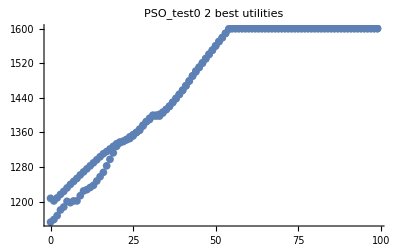

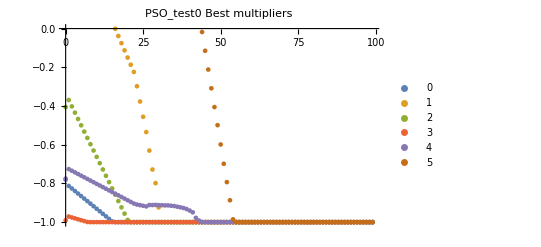

-Graphics3D-

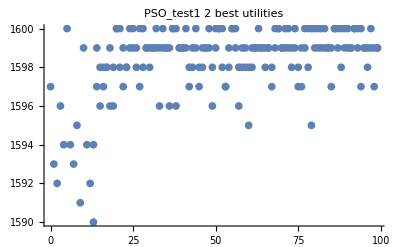

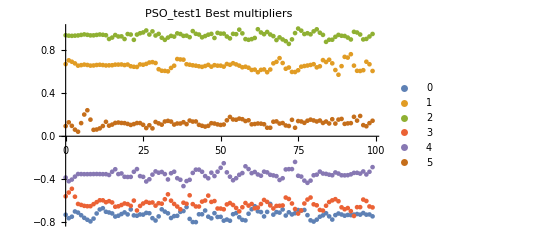

-Graphics3D-

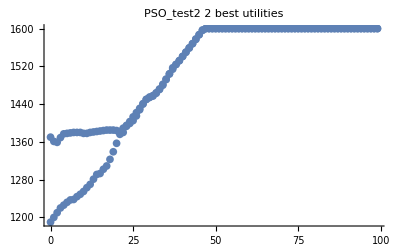

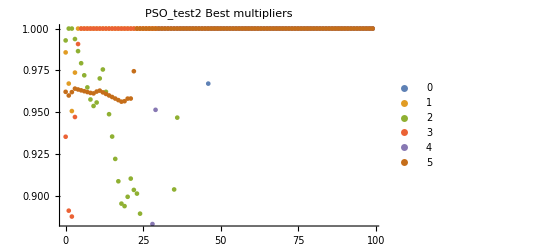

-Graphics3D-

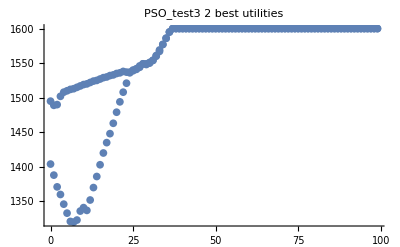

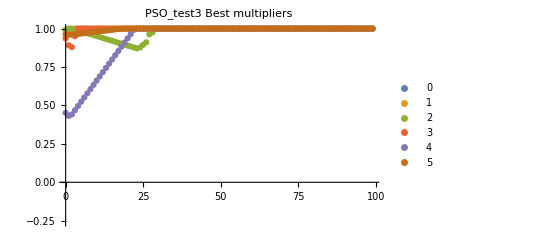

-Graphics3D-

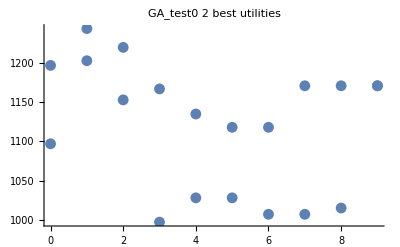

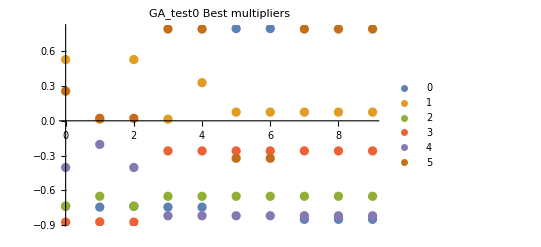

-Graphics3D-

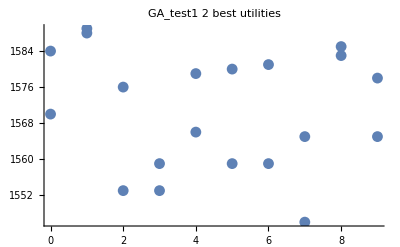

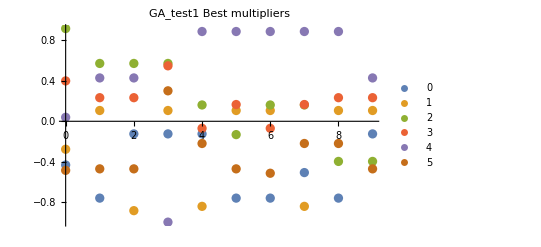

-Graphics3D-

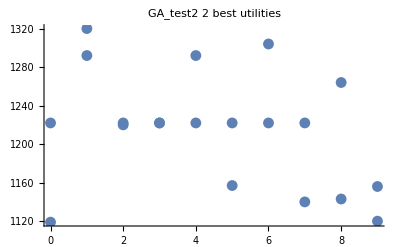

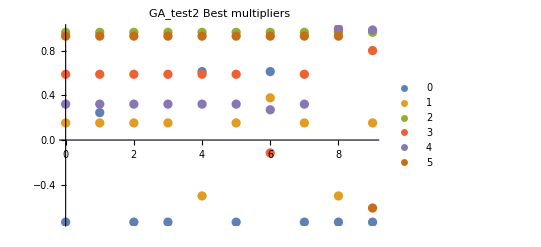

-Graphics3D-

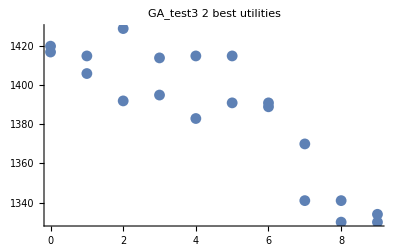

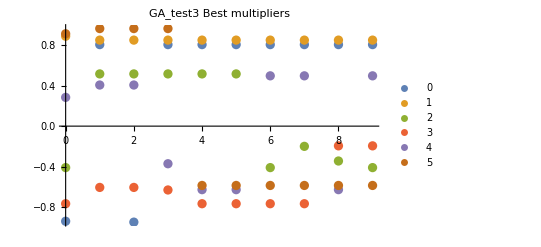

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
algorithms = {"PSO_test0", "PSO_test1", "PSO_test2", "PSO_test3", "GA_test0", "GA_test1","GA_test2", "GA_test3"};

Table[
ListPointPlot3D[Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_allUtilities.log"]}], "Table"], PlotRange-> All, PlotLabel-> StringJoin[i," all utilities"]] // Print
;

ListPlot[Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_twoBestUtilities.log"]}], "Table"], PlotLabel -> StringJoin[i," 2 best utilities"]]  // Print

;

in = Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_bestMultipliers.log"]}], "Table", FieldSeparators -> { ",", " "}];
ListPlot[Partition[in, Length[in]/6],PlotLegends->{0,1,2,3,4,5},PlotLabel->StringJoin[i," Best multipliers"]] // Print
, {i, algorithms}]
```